```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
paramColumnMap=<|"H0_mean"->"H0","q0_mean"->"q0","j0_mean"->"j0","Om0_mean"->"Om0","eps_mean"->"eps","wDE0_mean"->"wDE0","wDE0p_mean"->"wDE0p"|>;
```

```mathematica
(*Build the nested association for a single model's CSV file*)
BuildModelParams[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
datasetName->Association[KeyValueMap[Function[{oldKey,newKey},newKey->assocFull[oldKey]],paramColumnMap]]]],rows]]];
```

```mathematica
(*Master nested association:allParams["Model 1"]["DESI"]-><|"H0"->...,...|>*)
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParams[file]],mcmcFiles]];
```

```mathematica
(* ============================================================*)
(*Convenience accessors*)
(* ============================================================*)

(*List available models*)
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
AvailableModels[]
```

{Model 1,Model 2,Model 3}

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
(*(*Main getter:GetParams["Model 1","DESI"]->Association of params*)
GetParams[model_String,dataset_String]:=Module[{},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
allParams[model][dataset]];

GetParams::nomodel="Model `1` not found. Available models: `2`";
GetParams::nodataset="Dataset `1` not found for `2`. Available datasets: `3`";*)
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
(*Main getter:GetParams["Model 1","DESI"]->Association of params,including "j"*)
GetParams[model_String,dataset_String]:=Module[{baseParams},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
baseParams=allParams[model][dataset];
Append[baseParams,"j"->jModelMap[model]]];
```

### Model 1:

#### Desi Values

```mathematica
params1a=GetParams["Model 1","DESI"];
params1a["q0"]
params1a["Om0"]
params1a["eps"]
params1a["H0"]
```

-0.517033

0.498537

-0.0258394

68.2919

```mathematica
H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;
```

### Model 2:

#### Desi Values

```mathematica
params2a=GetParams["Model 2","DESI"];
params2a["q0"]
params2a["Om0"]
params2a["eps"]
params2a["H0"]
```

-0.49883

0.491401

-0.100239

68.5342

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 3:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Setup

```mathematica
zPlot=10;
zinitial=1000;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dh=(1+z)h'[z]- h[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

### Obtaining q(z)

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol},
params=GetParams[model,dataset];
odeQ={dq/. j->params["j"]/. ϵ->params["eps"],q[0]==params["q0"]};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Plots for each model, all datasets

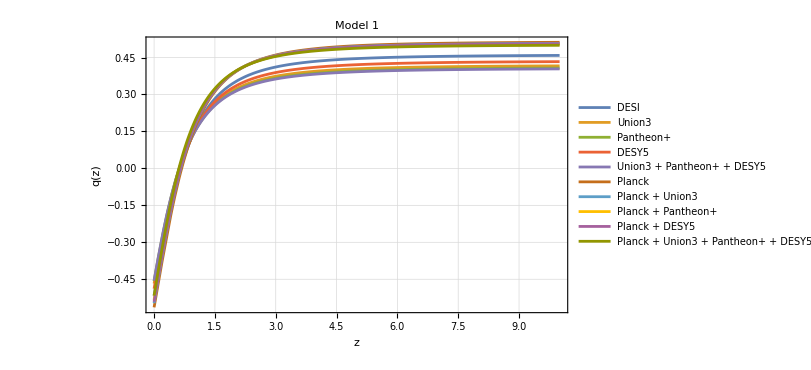

```mathematica
Plot[Evaluate[Table[qSolAllSets1[d][z],{d,Keys[qSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

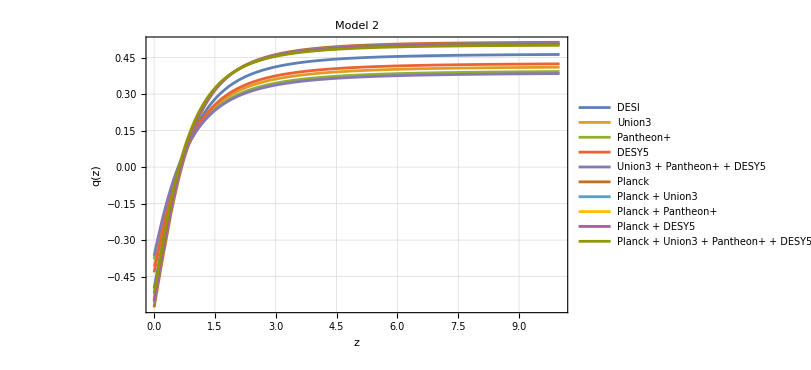

```mathematica
Plot[Evaluate[Table[qSolAllSets2[d][z],{d,Keys[qSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets2],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

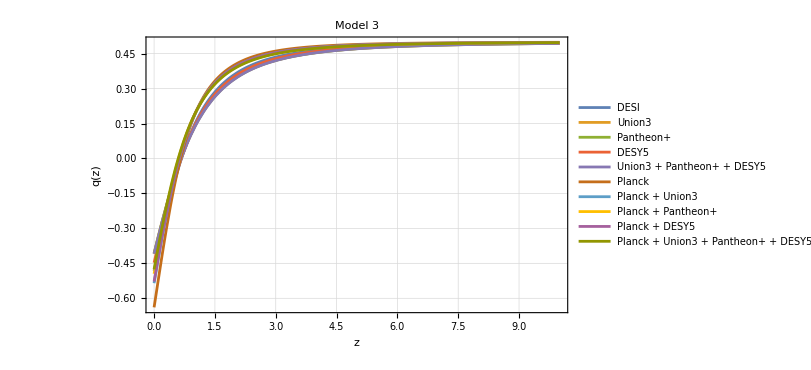

```mathematica
Plot[Evaluate[Table[qSolAllSets3[d][z],{d,Keys[qSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

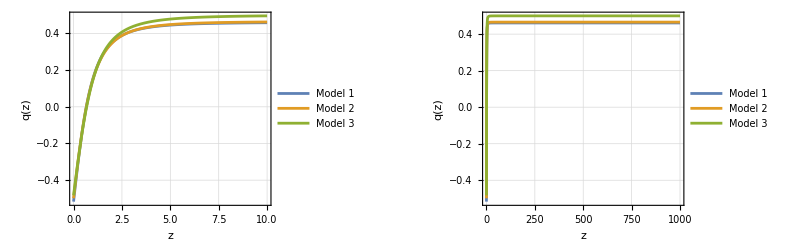

```mathematica
GraphicsRow[{
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

### Obtaining h(z)

```mathematica
SolveForh[model_String,dataset_String]:=
Module[{params,qFn,odeH,sol},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

odeH={(dh/. q->qFn)/. ϵ->params["eps"],h[0]==1};
sol=NDSolve[odeH,h,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
h/. sol[[1]]];
```

```mathematica
hSolAllSets1=Association[Map[#->SolveForh["Model 1",#]&,AvailableDatasets["Model 1"]]];
hSolAllSets2=Association[Map[#->SolveForh["Model 2",#]&,AvailableDatasets["Model 2"]]];
hSolAllSets3=Association[Map[#->SolveForh["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Plots for each model, all datasets

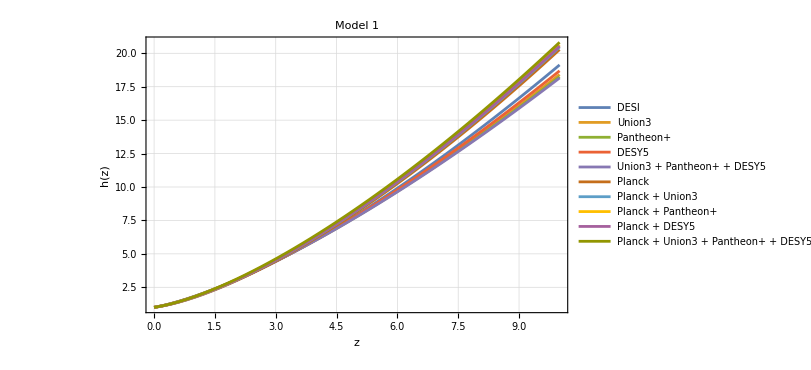

```mathematica
Plot[Evaluate[Table[hSolAllSets1[d][z],{d,Keys[hSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

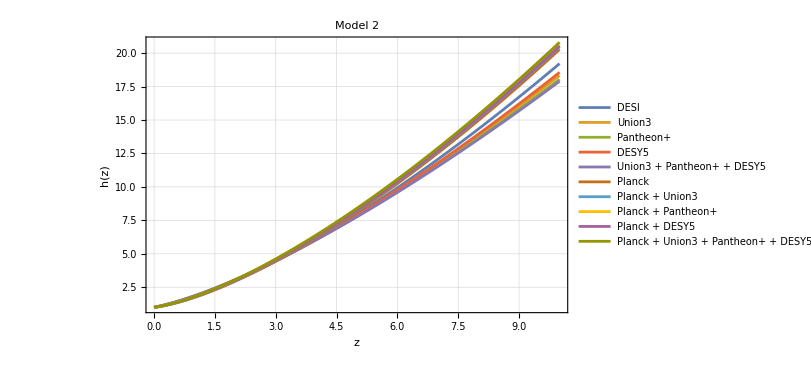

```mathematica
Plot[Evaluate[Table[hSolAllSets2[d][z],{d,Keys[hSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

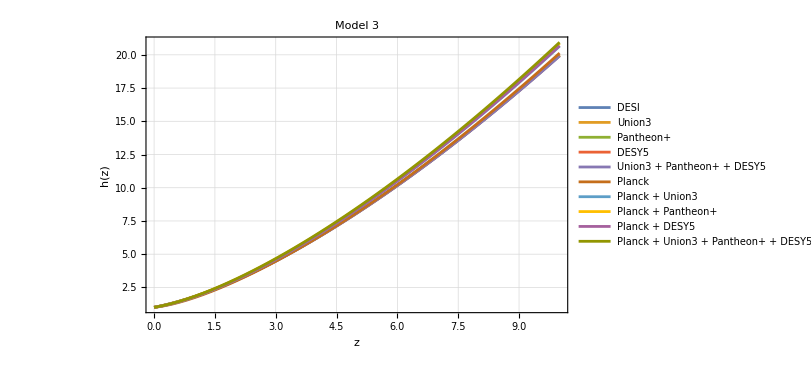

```mathematica
Plot[Evaluate[Table[hSolAllSets3[d][z],{d,Keys[hSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

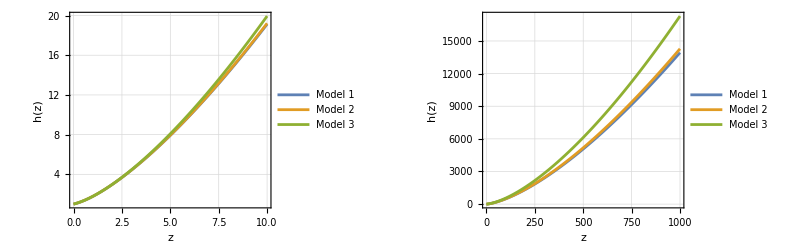

```mathematica
GraphicsRow[{
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","h(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","h(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

## Obtaining Background solution

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

1000

```mathematica
xin=-10^-14;
Ωin=0.999999997;
```

```mathematica
Table[qSolAllSets1[dataset][zinitial], {dataset,Keys[qSolAllSets3]}]
```

{0.461241,0.41875,0.409844,0.435914,0.406463,0.514422,0.509831,0.506433,0.50827,0.501985}

```mathematica
Keys[qSolAllSets3]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
SolveBackground[model_String,dataset_String]:=
Module[{params,qFn,z0,x0,Ω0,sol,xFn,ΩFn},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

z0=zinitial;
x0=xin;
Ω0=Ωin;

Block[{q,j,s,l,ϵ},
q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
(*Single integration:z0=zinitial down to 0,q now a known forcing function*)sol=NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
<|"x"->xFn,"Ω"->ΩFn,"z0"->z0,"zinitial"->zinitial|>];
```

```mathematica
SolveBackground[model_String,dataset_String]:=Module[{params,qFn,z0,x0,Ω0,sol,xFn,ΩFn,domainEnd},params=GetParams[model,dataset];
If[params===$Failed,Return[$Failed]];
qFn=SolveForq[model,dataset];
If[qFn===$Failed,Return[$Failed]];
z0=zinitial;
x0=xin;
Ω0=Ωin;
Block[{q,j,s,l,ϵ},q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
(*Check where the interpolating function's domain actually ends*)domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];
<|"x"->xFn,"Ω"->ΩFn,"z0"->z0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None]|>];
```

```mathematica
bgResultsModel1=Association[Map[#->SolveBackground["Model 1",#]&,AvailableDatasets["Model 1"]]];
```

DESI is stiff/diverges at z ≃ 113.991

Union3 is stiff/diverges at z ≃ 144.78

Pantheon+ is stiff/diverges at z ≃ 149.852

DESY5 is stiff/diverges at z ≃ 133.952

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 151.698

```mathematica
(*Summary table:dataset,qin,did it fail,at what z*)
Grid[Prepend[Table[{dataset,qSolAllSets1[dataset][zinitial],bgResultsModel1[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","q_in","Failed at z"}],Frame->All]
```

Dataset | q_in | Failed at z
DESI | 0.461241 | 113.991
Union3 | 0.41875 | 144.78
Pantheon+ | 0.409844 | 149.852
DESY5 | 0.435914 | 133.952
Union3 + Pantheon+ + DESY5 | 0.406463 | 151.698
Planck | 0.514422 | None
Planck + Union3 | 0.509831 | None
Planck + Pantheon+ | 0.506433 | None
Planck + DESY5 | 0.50827 | None
Planck + Union3 + Pantheon+ + DESY5 | 0.501985 | None

#### Plotting for converging solutions

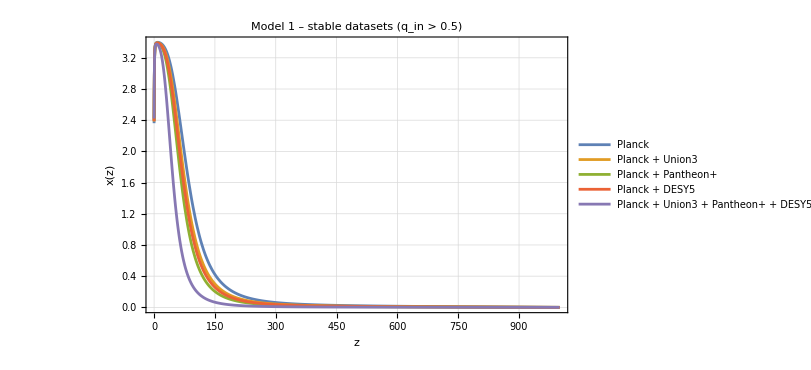

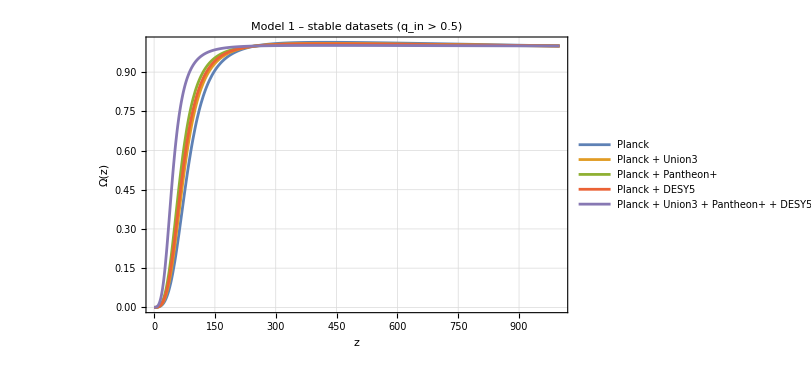

```mathematica
okDatasets=Select[AvailableDatasets["Model 1"],bgResultsModel1[#]["failedAtZ"]===None&];

(*Plot 3:successful datasets,z=0 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["x"][z],{d,okDatasets}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 1 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot 4:successful datasets,z=0 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["Ω"][z],{d,okDatasets}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 1 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

#### Plotting for converging solutions

```mathematica
failedDatasets=Select[AvailableDatasets["Model 1"],bgResultsModel1[#]["failedAtZ"]=!=None&];
```

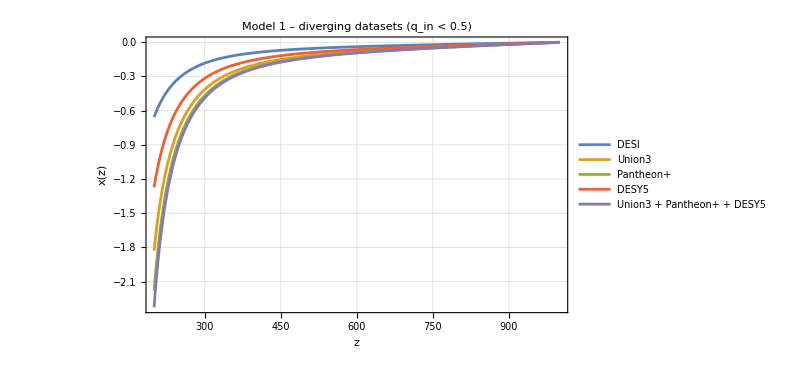

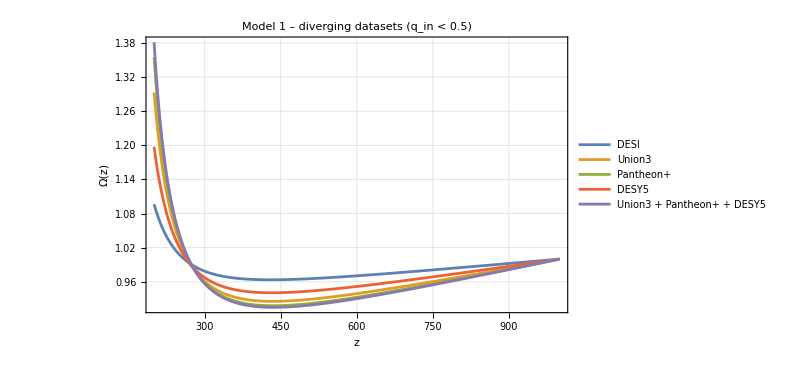

```mathematica
failedDatasets=Select[AvailableDatasets["Model 1"],bgResultsModel1[#]["failedAtZ"]=!=None&];
(*Plot 1:failed datasets,z=200 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["x"][z],{d,failedDatasets}]],{z,200,1000},PlotLegends->Placed[LineLegend[failedDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot 2:failed datasets,z=200 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["Ω"][z],{d,failedDatasets}]],{z,200,1000},PlotLegends->Placed[LineLegend[failedDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

## Obtaining Background solution old

#### Initial conditions

```mathematica
x0=-0.001;
Ω0=0.993243;
```

```mathematica
IC1a={zi,x0,Ω0,q0};
IC2a={zi,x0,Ω0,q0};
IC3a={zi,x0,Ω0,q0};
```

#### Module + models solutions

```mathematica
SolveBackground[jModel_,ICs_List, ϵVal_]:=
Module[{z0,x0,Ω0,q0,sExpr,lExpr,solFwd,solBwd, hsol, xFn, ΩFn, qFn, hFn},
{z0,x0,Ω0,q0}=ICs;

Block[{j,s,l, ϵ},
ϵ=ϵVal;

j[z_]=jModel;
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]/. q'[z]->Solve[dq,q'[z]][[1,1,2]]//Simplify;

(*Forward:z0->0*)
solFwd=NDSolve[{dx,dΩ,dq,x[z0]==x0,Ω[z0]==Ω0,q[z0]==q0},{x,Ω,q},{z,z0,0},PrecisionGoal->10, AccuracyGoal->10][[1]];
(*Backward:z0->zinitial*)
solBwd=NDSolve[{dx,dΩ,dq,x[z0]==x0,Ω[z0]==Ω0,q[z0]==q0},{x,Ω,q},{z,z0,zinitial},PrecisionGoal->10, AccuracyGoal->10][[1]];

xFn=With[{fwd=x/. solFwd,bwd=x/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];
ΩFn=With[{fwd=Ω/. solFwd,bwd=Ω/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];
];


<|"x"->xFn,"Ω"->ΩFn,"z0"->z0, "zinitial"->zinitial|>
];
```

```mathematica
sol1a=SolveBackground[j1[z],IC1a, ϵ1a];
replacements1a={x->sol1a["x"], Ω->sol1a["Ω"],q->qFn1a ,h->hFn1a,H->HFn1a, ϵ->ϵ1a,j->j1,Ωm0->Ωm01a,H0->H01a};
```

```mathematica
sol2a=SolveBackground[j2[z],IC2a, ϵ2a];
replacements2a={x->sol2a["x"], Ω->sol2a["Ω"],q->qFn2a ,h->hFn1a,H->HFn2a, ϵ->ϵ2a,j->j2,Ωm0->Ωm02a,H0->H02a};
```

```mathematica
sol3a=SolveBackground[j3[z],IC3a, ϵ3a];
replacements3a={x->sol3a["x"], Ω->sol3a["Ω"],q->qFn3a ,h->hFn1a,H->HFn3a, ϵ->ϵ3a,j->j3,Ωm0->Ωm03a,H0->H03a};
```

#### LCDM solution:

```mathematica
(* ΛCDM parameters *)
Ωm0LCDM=0.3;
hLCDM[z_]:= Sqrt[Ωm0LCDM(1+z)^3+(1-Ωm0LCDM)];
HLCDM[z_]=H0 hLCDM[z];
ΩΛ0=1-Ωm0LCDM;
```

```mathematica
qLCDM[z_]:=-1+(1+z)HLCDM'[z]/HLCDM[z];
```

```mathematica
xLCDM[z_]:=0 
ΩLCDM[z_]:= (Ωm0LCDM(1+z)^3)/(Ωm0LCDM(1+z)^3+ΩΛ0)
```

```mathematica
solLCDM=<|"x"->xLCDM[z],"Ω"->ΩLCDM[z],"q"->qLCDM[z],"h"->hLCDM[z],"z0"->z0|>;
LCDMreplacements={H[z]->HLCDM[z], h->hLCDM,q[z]->qLCDM[z], j[z]->1, x[z]->xLCDM[z], Ω[z]->ΩLCDM[z],Ωm0->Ωm0LCDM};
```

### Plotting x, Ω for all models

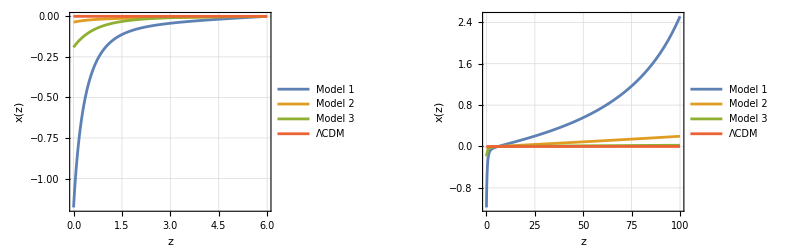

```mathematica
GraphicsRow[{
Plot[
Evaluate[{sol1a["x"][z],sol2a["x"][z],sol3a["x"][z],xLCDM[z]}],{z,0,zi},
ImageSize->500,
Frame->True,FrameLabel->{"z","x(z)"}, GridLines->Automatic,
PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}],

Plot[
Evaluate[{sol1a["x"][z],sol2a["x"][z],sol3a["x"][z],xLCDM[z]}],{z,0,zinitial},
ImageSize->500,
Frame->True,FrameLabel->{"z","x(z)"}, GridLines->Automatic,
PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
},ImageSize->Full]
```

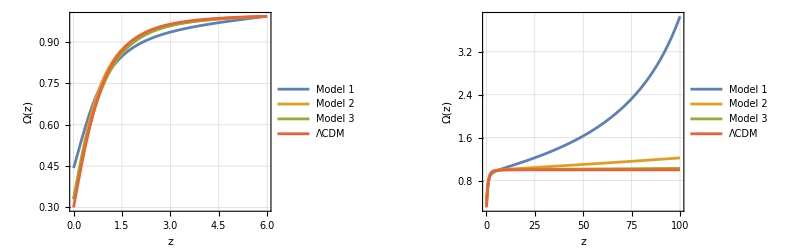

```mathematica
GraphicsRow[{
Plot[
Evaluate[{sol1a["Ω"][z],sol2a["Ω"][z],sol3a["Ω"][z],ΩLCDM[z]}],{z,0,zi},
ImageSize->500,
Frame->True,FrameLabel->{"z","Ω(z)"}, GridLines->Automatic,
PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}],

Plot[
Evaluate[{sol1a["Ω"][z],sol2a["Ω"][z],sol3a["Ω"][z],ΩLCDM[z]}],{z,0,zinitial},
ImageSize->500,
Frame->True,FrameLabel->{"z","Ω(z)"}, GridLines->Automatic,
PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
},ImageSize->Full]
```

```mathematica
{sol1a["Ω"][z],sol2a["Ω"][z],sol3a["Ω"][z], ΩLCDM[z]}/.z->0
{sol1a["Ω"][z],sol2a["Ω"][z],sol3a["Ω"][z], ΩLCDM[z]}/.z->zinitial
```

{0.442852,0.32985,0.32987,0.3}

{3.86101,1.22277,1.02686,0.999998}

```mathematica
{Ωm01a, Ωm02a, Ωm03a}
```

{0.498537,0.491401,0.503911}

### Matter density (Ω_m) Analysis

```mathematica
Ωm[z_] :=Ωm0/h[z]^2(1+z)^3;
```

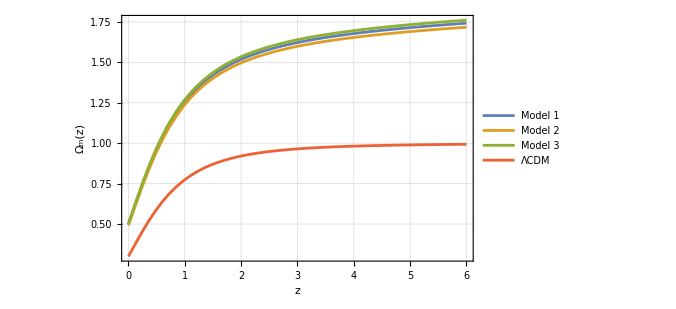

```mathematica
matterDensityCombined=Plot[Evaluate[
{Ωm[z]/. replacements1a,Ωm[z]/. replacements2a,Ωm[z]/. replacements3a,Ωm[z]/. LCDMreplacements}],
{z,0,zi},
ImageSize->500,GridLines->Automatic,
PlotRange->{{0,zi},Automatic},Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
```

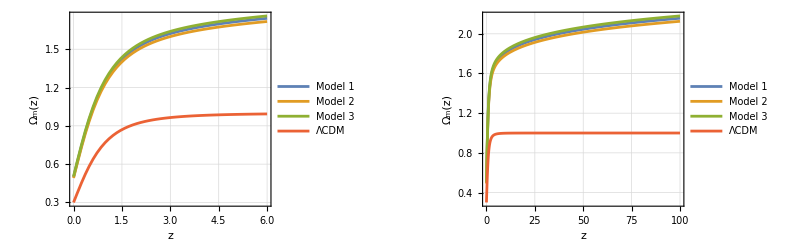

```mathematica
GraphicsRow[
{
Plot[Evaluate[
{Ωm[z]/. replacements1a,Ωm[z]/. replacements2a,Ωm[z]/. replacements3a,Ωm[z]/. LCDMreplacements}],
{z,0,zi},
GridLines->Automatic,
PlotRange->{{0,zi},Automatic},Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}, ImageSize->Full],
Plot[Evaluate[
{Ωm[z]/. replacements1a,Ωm[z]/. replacements2a,Ωm[z]/. replacements3a,Ωm[z]/. LCDMreplacements}],
{z,0,zinitial},
GridLines->Automatic,
PlotRange->{{0,zinitial},Automatic},Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}, ImageSize->Full]
}, ImageSize->Full]
```

```mathematica
(1+z)^3/h[z]^2/.replacements3a/.z->6
```

3.49416

### DE equation of state

```mathematica
wDE[z_]:=(2q[z]-1)/(3(1-Ωm[z]));
```

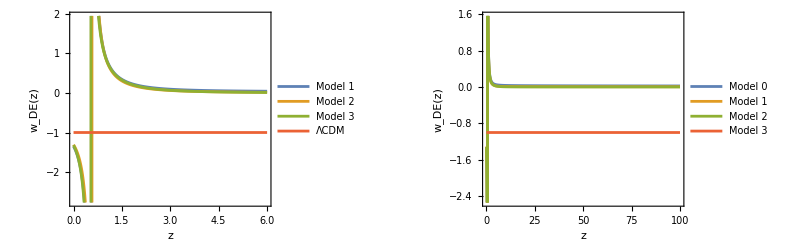

```mathematica
GraphicsRow[{
Plot[Evaluate[{wDE[z]/.replacements1a,
wDE[z]/.replacements2a,wDE[z]/.replacements3a,wDE[z]/. LCDMreplacements}],{z,0,zi},ImageSize->Full,
PlotRange->{{0,zi},Automatic},Frame->True,FrameLabel->{"z","w_DE(z)"},PlotLegends->Placed[
LineLegend[{"Model 1","Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}],
Plot[Evaluate[{wDE[z]/.replacements1a,
wDE[z]/.replacements2a,wDE[z]/.replacements3a,wDE[z]/. LCDMreplacements}],{z,0,zinitial},ImageSize->Full,
PlotRange->{{0,zinitial},Automatic},Frame->True,FrameLabel->{"z","w_DE(z)"},PlotLegends->Placed[
LineLegend[{"Model 0","Model 1","Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
}, ImageSize->Full]
```